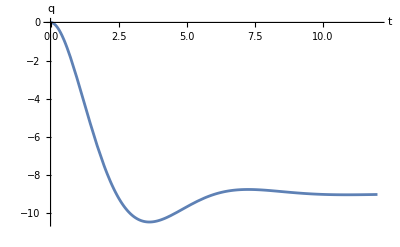

```mathematica
{L,R,c}={1,1,1}; TMax=12;
qSol=NDSolveValue[{L q''[t]+R q'[t]+q[t]/c +9==0,q[0]==0,q'[0]==0},q,{t,0, TMax}];
Plot[qSol[t],{t, 0, TMax},PlotRange->All,AxesLabel->{"t","q"}]
```